```mathematica
eqs={k*(G+n-1)-ga*Fm/Fp*Cos[2*ψ]-gp*Fm/Fp*Sin[2*ψ],-w+a*k*(G+n-1)+ga*Fm/Fp*Sin[2*ψ]-gp*Fm/Fp*Cos[2*ψ],k*(G-n-1)-ga*Fp/Fm*Cos[2*ψ]+gp*Fp/Fm*Sin[2*ψ],-w+a*k*(G-n-1)-ga*Fp/Fm*Sin[2*ψ]-gp*Fp/Fm*Cos[2*ψ],g*Λ-g*G-G*(Fp^2+Fm^2)-n*(Fp^2-Fm^2),-gd*n-G*(Fp^2-Fm^2)-n*(Fp^2+Fm^2)};
vars={Fp,Fm,ψ,w,G,n}
```

{Fp,Fm,ψ,w,G,n}

```mathematica
Solve[eqs==0,vars, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{k (-1+G+n)-(Fm ga Cos[2 ψ])/Fp-(Fm gp Sin[2 ψ])/Fp,a k (-1+G+n)-w-(Fm gp Cos[2 ψ])/Fp+(Fm ga Sin[2 ψ])/Fp,k (-1+G-n)-(Fp ga Cos[2 ψ])/Fm+(Fp gp Sin[2 ψ])/Fm,a k (-1+G-n)-w-(Fp gp Cos[2 ψ])/Fm-(Fp ga Sin[2 ψ])/Fm,-(Fm^2+Fp^2) G-g G-(-Fm^2+Fp^2) n+g Λ,-(-Fm^2+Fp^2) G-(Fm^2+Fp^2) n-gd n}==0,{Fp,Fm,ψ,w,G,n},ℝ]

```mathematica
tst={x+y-2,x-y-5}
```

{-2+x+y,-5+x-y}

```mathematica
Solve[tst==0,{x,y}]
```

{{x→7/2,y→-3/2}}

```mathematica
tst==0
```

{-2+x+y,-5+x-y}==0

## Test of formulae

```mathematica
(*Parameters*)
a=2;
k=300;
g=1;
gd=50;
ga=-0.01;
gp=34.611;
Λ=1.8;

a=5;
k=1000;
g=1;
gd=1/(5*10^-3);
ga=-0.000001;
gp=0.1;
Λ=1.6;
```

```mathematica
Clear[a,k,g,gd,ga,gp,Λ];
```

```mathematica
equations={(g*(Λ-G)*G+gd*n^2)*((G-1)*(ga^2+gp^2)+A)/(2*n*gp*(gp-a*ga))-g*(Λ-G)*n+gd*G*n,
k^2*((G-1)*(2*ga*gp+a*(gp^2-ga^2))-a*A)/ga/gp-((G-1)*(ga^2+2*a*ga*gp-gp^2)-A)/((G-1-n)*(G-1+n))};
Asub={A-> -Sqrt[(G-1)^2*(ga^2+gp^2)^2-4*n^2*ga*gp*(ga+a*gp)*(gp-a*ga)]};
```

```mathematica
solution=Solve[(equations/.Asub)==0,{G,n},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{G→0.505534,n→-0.494466},{G→0.505534,n→0.494466},{G→0.996967,n→-0.00303351},{G→0.996967,n→0.00303351},{G→1.,n→-3.11001×10^-12},{G→1.,n→3.11001×10^-12},{G→1.,n→-5.59517×10^-11},{G→1.,n→5.59517×10^-11},{G→1.,n→-1.5044×10^-7},{G→1.,n→1.5044×10^-7}}

```mathematica
ind=7;
sol=Join[solution[[ind]],
{Fp-> (Sqrt[(g*(Λ-G)-gd*n)/(2*(G+n))]/.solution[[ind]]),
Fm-> (Sqrt[(g*(Λ-G)+gd*n)/(2*(G-n))]/.solution[[ind]]),
ψ-> (1/2*ArcTan[((G-1)*(ga^2+gp^2)+A)/(2*n*gp*(ga+a*gp))]/.Asub/.solution[[ind]]),
w-> (k/ga*(-(G-1)*(gp-a*ga)+n*(ga+a*gp)*((G-1)*(ga^2+gp^2)+A)/(2*n*gp*(ga+a*gp)))/.Asub/.solution[[ind]])
}
]
```

{G→1.,n→-5.59517×10^-11,Fp→0.547723,Fm→0.547723,ψ→2.79773×10^-7,w→0.100005}

```mathematica
eqs/.sol//MatrixForm//Chop
```

(0.00998092
-34.711
0.0100197
-34.711
0.2
-8.39276×10^-9)

## Roman Approach

```mathematica
(*ClearAll["Global`*"]*)
eq1=κ(G+d - 1)-γa Sqrt[qm/qp] Cos[2 ψ]- γp Sqrt[qm/qp]Sin[2 ψ];
eq2= κ  α(G+d - 1)+γa Sqrt[qm/qp] Sin[2 ψ]-γp Sqrt[qm/qp]Cos[2 ψ]-ω;
eq3=κ (G-d - 1)-γa Sqrt[qp/qm]Cos[2 ψ]+ γp Sqrt[qp/qm] Sin[2 ψ];
eq4=κ  α(G-d - 1)-γa Sqrt[qp/qm]Sin[2 ψ]-γp Sqrt[qp/qm]Cos[2 ψ]-ω;
eq5=-γ(G -Λ)-γ(G+d) qp-γ(G-d) qm;
eq6=-γd d-γ(G+d) qp+γ(G-d) qm;
solGd=Solve[{eq5==0,eq6==0},{G,d}][[1]]
```

{G→-(3.30303 (50.+1. qm+1. qp))/(-50.-51. qm-51. qp-4. qm qp),d→-(3.30303 (1. qm^2-2. qm qp+1. qp^2))/((1. qm-1. qp) (-50.-51. qm-51. qp-4. qm qp))}

```mathematica
(eq2-α*eq1)/.solGd//FullSimplify//Solve[#==0,ω]&//FullSimplify
Solve[(eq4-α*eq3/.solGd)==0,ω]//FullSimplify
Solve[(eq4/.solGd)==0,ω]//FullSimplify
```

{{ω→√(qm/qp) ((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])}}

{{ω→√(qp/qm) ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ])}}

{{ω→α κ (-1+((2 qp γ+γd) Λ)/(γd+qp (γ+γd)+qm (γ+4 qp γ+γd)))-√(qp/qm) (γp Cos[2 ψ]+γa Sin[2 ψ])}}

```mathematica
(*cosinsubs={Cos[2ψ]->a,Sin[2ψ]->Sqrt[1-a^2]};*)
cosinsubs={Sin[2ψ]->a,Cos[2ψ]->Sqrt[1-a^2]};
(*cosinsubs={Sin[2ψ]->2*a/(1+a^2),Cos[2ψ]->(1-a^2)/(1+a^2)};*)
solω1=Simplify[Solve[(eq2/.cosinsubs/.solGd)==0,ω],Assumptions->qm>0&&qp>0&&-1<a<1][[1,1]];
solω2=Simplify[Solve[(eq4/.cosinsubs/.solGd)==0,ω],Assumptions->qm>0&&qp>0&&-1<a<1][[1,1]];
Eq1=(eq1/.cosinsubs/.solGd);
Eq2=(eq3/.cosinsubs/.solGd);
Eq3=Simplify[(eq2-eq4)/.cosinsubs/.solGd,Assumptions->qm>0&&qp>0&&a<1&&a>-1];
```

```mathematica
γa=-0.016*2*Pi;
γ=1.;
γp=8.*2*Pi;
κ=1000.;
γd=50;
α=5.;
Λ=2.;
qp0=0.9;
qm0=0.1;
a0=0.1;

γa=-0.01;
γ=1.;
γp=53.366992312063097;
κ=300.;
γd=50.;
α=3.;
Λ=3.303030303030303;
qp0=0.9;
qm0=0.1;
a0=-0.1;

solQpm=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{qm,qm0,N[10^-8],3},{qp,qp0,N[10^-8],3},{a,a0,-1.,1.}}]
solGd/.solQpm;
(Abs[d]/.%)≥ (G-1)/.%
solω1/.solQpm;
solω2/.solQpm;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{qm→1.15157,qp→1.15157,a→-3.57753×10^-9}

True

```mathematica
answrs={qp,qm,ArcSin[a]/2,ω,G,d}/.solω1/.solGd/.solQpm;
answrs//MatrixForm
```

(0.917982
0.0675131
-0.0863283
-25.2681
1.01455
-0.0169234)

```mathematica
sol=Flatten[{solGd/.solQpm,solQpm,solω1/.solQpm}]
```

{G→0.999967,d→-4.16759×10^-10,qm→1.15157,qp→1.15157,a→-3.57753×10^-9,ω→-53.397}

```mathematica
matmat=(M//TrigReduce)/.cosinsubs/.{Gs-> G, ds-> d,Qp-> qp,Qm-> qm}/.sol
```

{{-0.0100001,-53.367,0.0100002,53.367,321.934,321.934},{53.367,-0.0100001,-53.367,0.0100002,965.801,965.801},{0.00999981,53.367,-0.00999987,-53.367,321.934,-321.934},{-53.367,0.00999981,53.367,-0.00999987,965.801,-965.801},{-2.14615,0,-2.14615,0,-3.30314,-3.05587×10^-8},{-2.14615,0,2.14615,0,-3.05587×10^-8,-52.3031}}

```mathematica
{Eq1,Eq2,Eq3}/.solGd//MatrixForm
{eq5,eq6}/.solGd/.solQpm//MatrixForm
```

(4.70625×10^-11
3.39749×10^-11
-3.19302×10^-11)

(0.
0.)

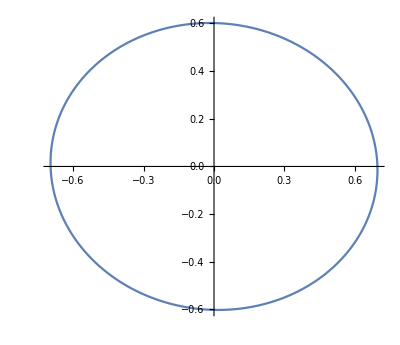

```mathematica
Ep =answrs[[1]];
Em = answrs[[2]];
p =answrs[[3]];
ParametricPlot[{Re[(Ep*Exp[I*(t+p)]+Em*Exp[I*(t-p)])/Sqrt[2]],Re[(Ep*Exp[I*(t+p)]-Em*Exp[I*(t-p)])/Sqrt[2]/I]},{t,0,2π}]
```

#### Linearization

```mathematica
ClearAll["Global`*"];
eq1=κ(1+I α)(G+d-1)Fp-(γa+I γp)Fm;
eq2=κ(1+I α)(G-d-1)Fm-(γa+I γp)Fp;
eq3=γ(Λ-G)-γ G(Abs[Fp]^2+Abs[Fm]^2)-γ d (Abs[Fp]^2-Abs[Fm]^2);
eq4=-γd d-γ G(Abs[Fp]^2-Abs[Fm]^2)-γ d (Abs[Fp]^2+Abs[Fm]^2);
eqns={eq1,eq2,eq3,eq4};
linsub={Fp-> (Sqrt[Qp]+ap)*Exp[I ω t+I ψ],Fm-> (Sqrt[Qm]+am)*Exp[I ω t-I ψ], G-> Gs+Δ,d-> ds+δ};
statsub={Fp-> Sqrt[Qp]*Exp[I ω t+I ψ],Fm-> Sqrt[Qm]*Exp[I ω t-I ψ], G-> Gs,d-> ds};
eqsub={(eq1/.statsub)-ω*Exp[I ω t+I ψ]-> 0, (eq2/.statsub)-ω*Exp[I ω t-I ψ]-> 0,(eq3/.statsub//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&//Expand)-> 0,(eq4/.statsub//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&//Expand)-> 0};
v2diff={ap,am,Δ,δ};
```

```mathematica
mults={Exp[I ω t+I ψ],Exp[I ω t-I ψ],1,1};
addrights={(Sqrt[Qp]+ap)*Exp[I ω t+I ψ]*I*ω,(Sqrt[Qm]+am)*Exp[I ω t-I ψ]*I*ω,0,0};
lineqs=Table[((eqns[[i]]/.linsub)-addrights[[i]])/mults[[i]]//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&//Expand,{i,1,4}]
```

{-am ⅇ^(-2 ⅈ ψ) γa-ⅇ^(-2 ⅈ ψ) √Qm γa-ⅈ am ⅇ^(-2 ⅈ ψ) γp-ⅈ ⅇ^(-2 ⅈ ψ) √Qm γp-ap κ+ap ds κ+ap Gs κ-√Qp κ+ds √Qp κ+Gs √Qp κ-ⅈ ap α κ+ⅈ ap ds α κ+ⅈ ap Gs α κ-ⅈ √Qp α κ+ⅈ ds √Qp α κ+ⅈ Gs √Qp α κ+ap δ κ+√Qp δ κ+ⅈ ap α δ κ+ⅈ √Qp α δ κ+ap Δ κ+√Qp Δ κ+ⅈ ap α Δ κ+ⅈ √Qp α Δ κ-ⅈ ap ω-ⅈ √Qp ω,-ap ⅇ^(2 ⅈ ψ) γa-ⅇ^(2 ⅈ ψ) √Qp γa-ⅈ ap ⅇ^(2 ⅈ ψ) γp-ⅈ ⅇ^(2 ⅈ ψ) √Qp γp-am κ-am ds κ+am Gs κ-√Qm κ-ds √Qm κ+Gs √Qm κ-ⅈ am α κ-ⅈ am ds α κ+ⅈ am Gs α κ-ⅈ √Qm α κ-ⅈ ds √Qm α κ+ⅈ Gs √Qm α κ-am δ κ-√Qm δ κ-ⅈ am α δ κ-ⅈ √Qm α δ κ+am Δ κ+√Qm Δ κ+ⅈ am α Δ κ+ⅈ √Qm α Δ κ-ⅈ am ω-ⅈ √Qm ω,-Gs γ-γ Δ+γ Λ+ds γ Abs[am+√Qm]^2-Gs γ Abs[am+√Qm]^2+γ δ Abs[am+√Qm]^2-γ Δ Abs[am+√Qm]^2-ds γ Abs[ap+√Qp]^2-Gs γ Abs[ap+√Qp]^2-γ δ Abs[ap+√Qp]^2-γ Δ Abs[ap+√Qp]^2,-ds γd-γd δ-ds γ Abs[am+√Qm]^2+Gs γ Abs[am+√Qm]^2-γ δ Abs[am+√Qm]^2+γ Δ Abs[am+√Qm]^2-ds γ Abs[ap+√Qp]^2-Gs γ Abs[ap+√Qp]^2-γ δ Abs[ap+√Qp]^2-γ Δ Abs[ap+√Qp]^2}

```mathematica
asub={ap-> apr+I api,am-> amr+ I ami};
simplylineqs=lineqs/.asub//ComplexExpand//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&;
rightpart={Simplify[Re[simplylineqs[[1]]//Expand],Assumptions-> Element[_,Reals]]//Expand,Simplify[Im[simplylineqs[[1]]//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Re[simplylineqs[[2]]//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Im[simplylineqs[[2]]//Expand],Assumptions-> Element[_,Reals]]//Expand,simplylineqs[[3]]//Expand,simplylineqs[[4]]//Expand};
```

```mathematica
vars = {apr,api,amr,ami,Δ,δ};
M=Table[CoefficientList[rightpart[[i]],vars,{2,2,2,2,2,2}][[1+Boole[j==1],1+Boole[j==2],1+Boole[j==3],1+Boole[j==4],1+Boole[j==5],1+Boole[j==6]]],{i,1,6},{j,1,6}];
```

```mathematica
M//MatrixForm
```

(-κ+ds κ+Gs κ | α κ-ds α κ-Gs α κ+ω | -γa Cos[2 ψ]-γp Sin[2 ψ] | γp Cos[2 ψ]-γa Sin[2 ψ] | √Qp κ | √Qp κ
-α κ+ds α κ+Gs α κ-ω | -κ+ds κ+Gs κ | -γp Cos[2 ψ]+γa Sin[2 ψ] | -γa Cos[2 ψ]-2 γp Cos[ψ] Sin[ψ] | √Qp α κ | √Qp α κ
-γa Cos[2 ψ]+γp Sin[2 ψ] | γp Cos[2 ψ]+γa Sin[2 ψ] | -κ-ds κ+Gs κ | α κ+ds α κ-Gs α κ+ω | √Qm κ | -√Qm κ
-γp Cos[2 ψ]-γa Sin[2 ψ] | -γa Cos[2 ψ]+γp Sin[2 ψ] | -α κ-ds α κ+Gs α κ-ω | -κ-ds κ+Gs κ | √Qm α κ | -√Qm α κ
-2 ds √Qp γ-2 Gs √Qp γ | 0 | 2 ds √Qm γ-2 Gs √Qm γ | 0 | -γ-Qm γ-Qp γ | Qm γ-Qp γ
-2 ds √Qp γ-2 Gs √Qp γ | 0 | -2 ds √Qm γ+2 Gs √Qm γ | 0 | Qm γ-Qp γ | -Qm γ-Qp γ-γd)

```mathematica
eqnss=eqns/.statsub//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&;
eqnss2={Simplify[Re[eqnss[[1]]*Exp[-I ω t-I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,Simplify[Im[eqnss[[1]]*Exp[-I ω t-I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Re[eqnss[[2]]*Exp[-I ω t+I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Im[eqnss[[2]]*Exp[-I ω t+I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,eqnss[[3]]//Expand,eqnss[[4]]//Expand};
eqnss2//Simplify//MatrixForm
```

((-1+ds+Gs) √Qp κ-√Qm γa Cos[2 ψ]-2 √Qm γp Cos[ψ] Sin[ψ]
(-1+ds+Gs) √Qp α κ-√Qm γp Cos[2 ψ]+√Qm γa Sin[2 ψ]
(-1-ds+Gs) √Qm κ-√Qp γa Cos[2 ψ]+√Qp γp Sin[2 ψ]
(-1-ds+Gs) √Qm α κ-√Qp γp Cos[2 ψ]-2 √Qp γa Cos[ψ] Sin[ψ]
-γ (ds (-Qm+Qp)+Gs (1+Qm+Qp)-Λ)
Gs (Qm-Qp) γ-ds (Qm γ+Qp γ+γd))

```mathematica
eqnss
```

{(-√Qm γa-ⅈ √Qm γp+(-1+ds+Gs) √Qp (1+ⅈ α) κ (Cos[2 ψ]+ⅈ Sin[2 ψ])) (Cos[ψ-t ω]-ⅈ Sin[ψ-t ω]),(-ⅈ (1+ds-Gs) √Qm (-ⅈ+α) κ-√Qp (γa+ⅈ γp) (Cos[2 ψ]+ⅈ Sin[2 ψ])) (Cos[ψ-t ω]-ⅈ Sin[ψ-t ω]),-Gs γ+ds Qm γ-Gs Qm γ-ds Qp γ-Gs Qp γ+γ Λ,-ds Qm γ+Gs Qm γ-ds Qp γ-Gs Qp γ-ds γd}

```mathematica
A=Det[M-s*IdentityMatrix[6]]//CoefficientList[#,s]&
```

{Qm γ^2 κ^4-2 ds^2 Qm γ^2 κ^4+2047+Qm 3 (γa^2 1^2+5+γa^2 1^2)+Qp γ γd (-γa Cos[2 ψ]+γp 1)^2 (γa^2 Cos[2 ψ]^2+γp^2 Cos[2 ψ]^2+2 γa γp Cos[ψ] Cos[2 ψ] Sin[ψ]-γa γp Cos[2 ψ] Sin[2 ψ]+2 γp^2 Cos[ψ] Sin[ψ] Sin[2 ψ]+γa^2 Sin[2 ψ]^2),5,1}
 |  |  |  |

```mathematica
A[[6]]//Simplify
```

γ+2 Qm γ+2 Qp γ+γd+4 κ-4 Gs κ

```mathematica
H={
{a1,a3,a5,0,0,0},
{a0,a2,a4,a6,0,0},
{0,a1,a3,a5,0,0},
{0,a0,a2,a4,a6,0},
{0,0,a1,a3,a5,0},
{0,0,a0,a2,a4,a6}
};
H//MatrixForm
```

(a1 | a3 | a5 | 0 | 0 | 0
a0 | a2 | a4 | a6 | 0 | 0
0 | a1 | a3 | a5 | 0 | 0
0 | a0 | a2 | a4 | a6 | 0
0 | 0 | a1 | a3 | a5 | 0
0 | 0 | a0 | a2 | a4 | a6)

```mathematica
dets=Table[Det[H[[1;;j,1;;j]]],{j,2,5}];
dets//Simplify//MatrixForm
```

(a1 a2-a0 a3
a1 a2 a3-a0 a3^2-a1^2 a4+a0 a1 a5
-a0 (a3^2 a4-a2 a3 a5+a0 a5^2)+a1^2 (-a4^2+a2 a6)+a1 (a2 a3 a4-a2^2 a5+2 a0 a4 a5-a0 a3 a6)
-a1^3 a6^2+a0 (-a3^2 a4 a5+a2 a3 a5^2-a0 a5^3+a3^3 a6)+a1^2 (-a4^2 a5+a3 a4 a6+2 a2 a5 a6)-a1 (a2^2 a5^2+a2 a3 (-a4 a5+a3 a6)+a0 a5 (-2 a4 a5+3 a3 a6)))

```mathematica
(dets[[4]]-dets[[3]]*a5)//Simplify
```

a6 (a0 a3^3-a1 a3 (a2 a3+2 a0 a5)+a1^2 (a3 a4+a2 a5)-a1^3 a6)

```mathematica
dets[[3]]-a4*dets[[2]]//Simplify
```

a0 a5 (a2 a3-a0 a5)+a1^2 a2 a6-a1 (a2^2 a5-a0 a4 a5+a0 a3 a6)

```mathematica
dets[[2]]-a3*dets[[1]]//Simplify
```

a1 (-a1 a4+a0 a5)

```mathematica
Expand[a0 a5 (a2 a3-a0 a5)+a1^2 a2 a6-a1 (a2^2 a5-a0 a4 a5+a0 a3 a6)]
```

-a1 a2^2 a5+a0 a2 a3 a5+a0 a1 a4 a5-a0^2 a5^2+a1^2 a2 a6-a0 a1 a3 a6

```mathematica
TestMat=Table[Random[Real],{i,1,6},{j,1,6}]
```

{{0.677517,0.232726,0.029356,0.850996,0.301431,0.848926},{0.713054,0.260037,0.509707,0.869024,0.413981,0.0924},{0.731208,0.748885,0.619961,0.664913,0.344366,0.166563},{0.553577,0.47379,0.611191,0.175111,0.782086,0.707329},{0.933674,0.942385,0.752729,0.856333,0.632243,0.0934586},{0.0396751,0.596296,0.122535,0.224435,0.625694,0.503896}}

```mathematica
TestMat={{0.6775172970730853,0.23272559355546446,0.029356045261020945,0.8509960465727234,0.30143129630356075,0.8489264805168724},{0.7130543420057717,0.2600372478789726,0.5097072819415147,0.8690239961046854,0.4139809045409873,0.09239999596144052},{0.7312077367278765,0.748884930691992,0.6199613172362929,0.6649129643086599,0.3443657753448619,0.16656331890697473},{0.5535768136327229,0.4737904046968728,0.6111911878166082,0.1751107197696297,0.7820855012928914,0.7073289712991265},{0.9336738907435229,0.9423851262141653,0.7527294560318705,0.8563329247264032,0.6322425944399621,0.09345864569729286},{0.039675114026098794,0.5962956768474306,0.12253531249844746,0.22443464959260742,0.6256942094851115,0.50389568088599}}
```

{{0.677517,0.232726,0.029356,0.850996,0.301431,0.848926},{0.713054,0.260037,0.509707,0.869024,0.413981,0.0924},{0.731208,0.748885,0.619961,0.664913,0.344366,0.166563},{0.553577,0.47379,0.611191,0.175111,0.782086,0.707329},{0.933674,0.942385,0.752729,0.856333,0.632243,0.0934586},{0.0396751,0.596296,0.122535,0.224435,0.625694,0.503896}}

```mathematica
Det[TestMat-s*IdentityMatrix[6]]//CoefficientList[#,s]&
```

{0.0291508,-0.202043,-0.653218,-0.987714,-0.468009,-2.86876,1}

### Tests

```mathematica
m={
{-1.0000*10^-2,-5.9948*10^1, 1.0000*10^-2, 5.9948*10^1, 3.1335*10^2, 3.1335*10^2},{5.9948*10^1,-1.0000*10^-2,-5.9948*10^1, 1.0000*10^-2, 9.4004*10^2, 9.4004*10^2},{1.0000*10^-2, 5.9948*10^1,-1.0000*10^-2,-5.9948*10^1, 3.1335*10^2,-3.1335*10^2},{-5.9948*10^1, 1.0000*10^-2, 5.9948*10^1,-1.0000*10^-2, 9.4004*10^2,-9.4004*10^2},{-2.0889, 0,-2.0889,0,-3.1819, 0},{-2.0889, 0, 2.0889,0,0,-5.2182*10^1}}
```

{{-0.01,-59.948,0.01,59.948,313.35,313.35},{59.948,-0.01,-59.948,0.01,940.04,940.04},{0.01,59.948,-0.01,-59.948,313.35,-313.35},{-59.948,0.01,59.948,-0.01,940.04,-940.04},{-2.0889,0,-2.0889,0,-3.1819,0},{-2.0889,0,2.0889,0,0,-52.182}}

```mathematica
m//MatrixForm
```

(-0.01 | -59.948 | 0.01 | 59.948 | 313.35 | 313.35
59.948 | -0.01 | -59.948 | 0.01 | 940.04 | 940.04
0.01 | 59.948 | -0.01 | -59.948 | 313.35 | -313.35
-59.948 | 0.01 | 59.948 | -0.01 | 940.04 | -940.04
-2.0889 | 0 | -2.0889 | 0 | -3.1819 | 0
-2.0889 | 0 | 2.0889 | 0 | 0 | -52.182)

```mathematica
CharacteristicPolynomial[m,s]
```

2.42092×10^-6+3.65606×10^8 s+2.14237×10^7 s^2+397554. s^3+17161.5 s^4+55.4039 s^5+s^6

```mathematica
matlabsub={Qp->1.151570203853719,Qm->  1.151570203856395,a->  0.000000000000165,Gs-> 0.999966666666802,ds-> 5.115888487337703*10^-14,ω-> -53.396992312098675}
```

{Qp→1.15157,Qm→1.15157,a→1.65×10^-13,Gs→0.999967,ds→5.11589×10^-14,ω→-53.397}

```mathematica
matM=(M//TrigReduce)/.{Sin[2ψ]-> a,Cos[2ψ]-> Sqrt[1-a^2]}/.matlabsub
```

{{-0.01,-53.367,0.01,53.367,321.934,321.934},{53.367,-0.01,-53.367,0.01,965.801,965.801},{0.01,53.367,-0.01,-53.367,321.934,-321.934},{-53.367,0.01,53.367,-0.01,965.801,-965.801},{-2.14615,0,-2.14615,0,-3.30314,2.67608×10^-12},{-2.14615,0,2.14615,0,2.67608×10^-12,-52.3031}}

```mathematica
γa=-0.01;
γ=1.;
γp=53.366992312063097;
κ=300.;
γd=50.;
α=3.;
Λ=3.303030303030303;
qp0=0.9;
qm0=0.1;
a0=-0.1;
```

```mathematica
CharacteristicPolynomial[matM,s]
```

-0.108668+2.11981×10^8 s+1.81612×10^7 s^2+267936. s^3+14330.8 s^4+55.6463 s^5+s^6

```mathematica
CharacteristicPolynomial[matmat,s]
```

66.8857+2.11981×10^8 s+1.81612×10^7 s^2+267936. s^3+14330.8 s^4+55.6463 s^5+s^6